```mathematica
ClearAll["Global`*"]
$PlotTheme = "Monochrome";
```

Porovnání analytického výsledku s numerickým

```mathematica
a:=5;
b:=3;
c:=10
```

```mathematica
re=Rectangle[{0,0},{a,b}]
```

Rectangle[{0,0},{5,3}]

```mathematica
{RectangleEigenvalues,RectangleEigenvectors}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈re,c];
```

```mathematica
{RectangleEigenvaluesFine,RectangleEigenvectorsFine}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u[x,y],
{x,y}∈re,
c, 
Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.3}}}}
];
```

```mathematica
N[NumericalSort[Flatten[Table[Pi^2*m^2/a^2+Pi^2*n^2/b^2,{m,1,c/2},{n,1,c/2}]]]]
RectangleEigenvalues
RectangleEigenvaluesFine
```

{1.49141,2.67576,4.64968,4.78128,5.96563,7.41317,7.93955,10.2644,10.703,10.9662,11.4487,13.4227,14.2561,16.1862,17.9407,19.1251,19.7392,21.099,23.8625,27.4156,27.8104,28.9947,30.9686,33.7321,37.2852}

{1.49141,2.67577,4.64977,4.78142,5.96578,7.41365,7.93978,10.266,10.7037,10.968}

{1.49153,2.67622,4.65358,4.78823,5.97312,7.43377,7.95144,10.3387,10.7345,11.0412}

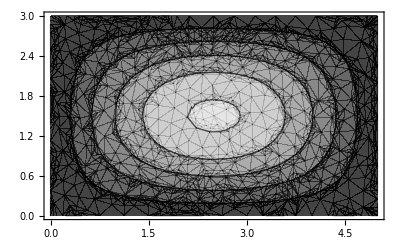
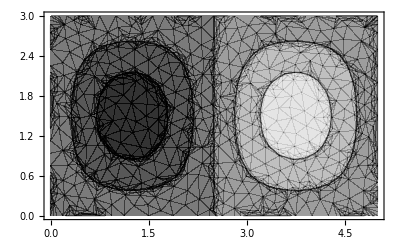
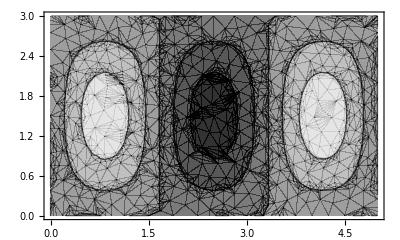
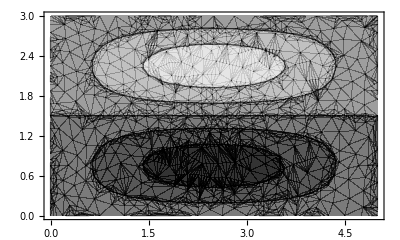
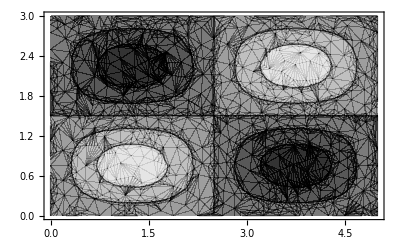
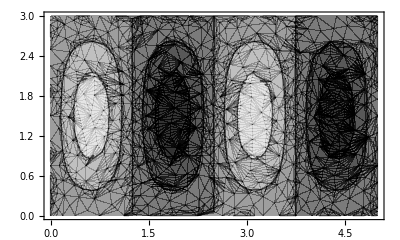
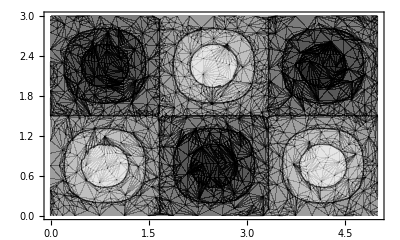
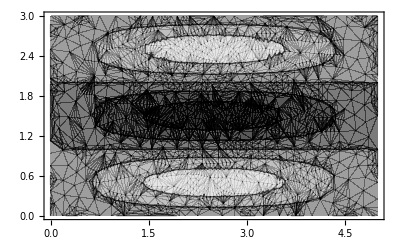

```mathematica
ContourPlot[#, {x, y} ∈re,AspectRatio->Automatic] & /@ RectangleEigenvectors
```